```mathematica
mainAssoc = stubbornForm6;
```

```mathematica
PartitionToSymbol2[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["p"<>end]]
```

```mathematica
GenerateAxioms2[assoc_, vertexCount_]:=Block[
{keysWith6Nodes=Select[Keys[assoc],With[{g=assoc[#]["graph"]},VertexCount[g]==vertexCount]&],
allPartitions=SetPartitions[vertexCount]},
Monitor[ 
Table[
With[
{key=First[Select[keysWith6Nodes,With[{g=assoc[#]["graph"]},IsPartitionGraph[g,part]]&]]},
mainAssoc[key,"colofour"]
]==PartitionToSymbol2[part],
{part,allPartitions}],part]
]
```

```mathematica
stubbornForm6[k,"colofour"]->Style[stubbornForm6[k,"colofour2"], If[ToString[stubbornForm6[k,"comp"]]=="GreaterEqual",Red,Green]]
```

Missing[KeyAbsent,k]→Missing[KeyAbsent,k]

```mathematica
baseGraphAxioma6Vars//Length
```

203

```mathematica
baseGraphAxioma6Vars // Length
```

203

```mathematica
prob=GenerateAxioms2[withRelations6, 6];
```

```mathematica
Take[prob,4]
```

{v1x2x3x4x5x6==p123456,v12x3x4x5x6+v13x2x4x5x6+v14x2x3x5x6+v15x2x3x4x6+v16x2x3x4x5+v1x2x3x4x5x6==p1x23456,v13x24x5x6+v13x25x4x6+v13x26x4x5+v13x2x4x5x6+v14x23x5x6+v14x25x3x6+v14x26x3x5+v14x2x3x5x6+v15x23x4x6+v15x24x3x6+v15x26x3x4+v15x2x3x4x6+v16x23x4x5+v16x24x3x5+v16x25x3x4+v16x2x3x4x5+v1x23x4x5x6+v1x24x3x5x6+v1x25x3x4x6+v1x26x3x4x5+v1x2x3x4x5x6==p12x3456,v12x3x4x5x6+v1x23x4x5x6+v1x24x3x5x6+v1x25x3x4x6+v1x26x3x4x5+v1x2x3x4x5x6==p13456x2}

```mathematica
probRep=Map[#[[1]]->#[[2]]&,prob];Take[probRep,4]
```

{v1x2x3x4x5x6→p123456,v12x3x4x5x6+v13x2x4x5x6+v14x2x3x5x6+v15x2x3x4x6+v16x2x3x4x5+v1x2x3x4x5x6→p1x23456,v13x24x5x6+v13x25x4x6+v13x26x4x5+v13x2x4x5x6+v14x23x5x6+v14x25x3x6+v14x26x3x5+v14x2x3x5x6+v15x23x4x6+v15x24x3x6+v15x26x3x4+v15x2x3x4x6+v16x23x4x5+v16x24x3x5+v16x25x3x4+v16x2x3x4x5+v1x23x4x5x6+v1x24x3x5x6+v1x25x3x4x6+v1x26x3x4x5+v1x2x3x4x5x6→p12x3456,v12x3x4x5x6+v1x23x4x5x6+v1x24x3x5x6+v1x25x3x4x6+v1x26x3x4x5+v1x2x3x4x5x6→p13456x2}

```mathematica
newVars=Select[Flatten[Map[ListofVars[#]&,prob]]//Sort,StringStartsQ[SymbolName[#],"p"]&];
```

```mathematica
Length[newVars]
```

203

```mathematica
sol=First[Solve[prob,newVars]];
```

```mathematica
(*sol=First[Solve[prob,baseGraphAxioma6Vars]];*)
```

```mathematica
GetCoeff[poly_]:=CoefficientList[poly,newVars]
```

```mathematica
mat62=CoefficientArrays[Map[#[[2]]&,sol],baseGraphAxioma6Vars][[2]];
```

```mathematica
mat6=Inverse[mat62];
```

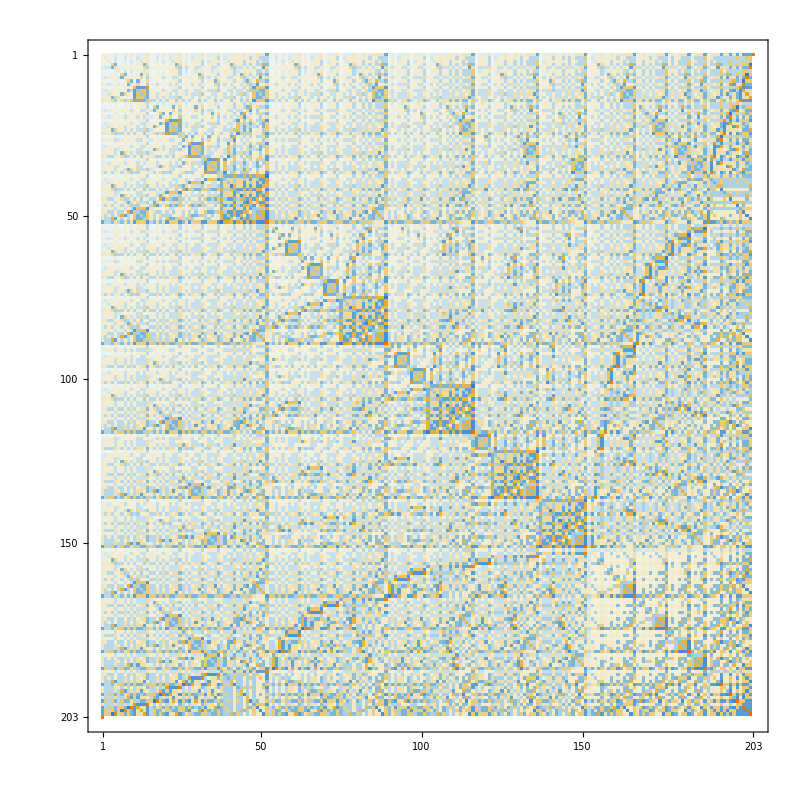

```mathematica
MatrixPlot[mat6,ImageSize->800]
```

```mathematica
Det[mat62]
```

6426666657455535625651051273371558183683294526786393206811525120

```mathematica
Det[mat6]
```

1/6426666657455535625651051273371558183683294526786393206811525120

```mathematica
-1/196689447424
```

-1/196689447424

```mathematica
FactorInteger[6426666657455535625651051273371558183683294526786393206811525120]
```

{{2,151},{3,37},{5,1}}

```mathematica
matrixForm[mat62]
```

matrixForm[SparseArray[<15125>, {203, 203}]]

```mathematica
Monitor[
Table[
stubbornForm6[k,"colofour2"]=Simplify[(CoefficientArrays[stubbornForm6[k,"colofour"],baseGraphAxioma6Vars][[2]].mat62).newVars]
,{k,Keys[stubbornForm6]}],
k];
```

```mathematica
stubbornForm6[0,"colofour2"]
```

p123456+6 p12345x6+6 p12346x5+21 p1234x56+26 p1234x5x6+6 p12356x4+21 p1235x46+26 p1235x4x6+21 p1236x45+26 p1236x4x5+34 p123x456+60 p123x45x6+60 p123x46x5+60 p123x4x56+77 p123x4x5x6+6 p12456x3+21 p1245x36+26 p1245x3x6+21 p1246x35+26 p1246x3x5+34 p124x356+60 p124x35x6+60 p124x36x5+60 p124x3x56+77 p124x3x5x6+21 p1256x34+26 p1256x3x4+34 p125x346+60 p125x34x6+60 p125x36x4+60 p125x3x46+77 p125x3x4x6+34 p126x345+60 p126x34x5+60 p126x35x4+60 p126x3x45+77 p126x3x4x5+21 p12x3456+60 p12x345x6+60 p12x346x5+87 p12x34x56+114 p12x34x5x6+60 p12x356x4+87 p12x35x46+114 p12x35x4x6+87 p12x36x45+114 p12x36x4x5+60 p12x3x456+114 p12x3x45x6+114 p12x3x46x5+114 p12x3x4x56+151 p12x3x4x5x6+6 p13456x2+21 p1345x26+26 p1345x2x6+21 p1346x25+26 p1346x2x5+34 p134x256+60 p134x25x6+60 p134x26x5+60 p134x2x56+77 p134x2x5x6+21 p1356x24+26 p1356x2x4+34 p135x246+60 p135x24x6+60 p135x26x4+60 p135x2x46+77 p135x2x4x6+34 p136x245+60 p136x24x5+60 p136x25x4+60 p136x2x45+77 p136x2x4x5+21 p13x2456+60 p13x245x6+60 p13x246x5+87 p13x24x56+114 p13x24x5x6+60 p13x256x4+87 p13x25x46+114 p13x25x4x6+87 p13x26x45+114 p13x26x4x5+60 p13x2x456+114 p13x2x45x6+114 p13x2x46x5+114 p13x2x4x56+151 p13x2x4x5x6+21 p1456x23+26 p1456x2x3+34 p145x236+60 p145x23x6+60 p145x26x3+60 p145x2x36+77 p145x2x3x6+34 p146x235+60 p146x23x5+60 p146x25x3+60 p146x2x35+77 p146x2x3x5+21 p14x2356+60 p14x235x6+60 p14x236x5+87 p14x23x56+114 p14x23x5x6+60 p14x256x3+87 p14x25x36+114 p14x25x3x6+87 p14x26x35+114 p14x26x3x5+60 p14x2x356+114 p14x2x35x6+114 p14x2x36x5+114 p14x2x3x56+151 p14x2x3x5x6+34 p156x234+60 p156x23x4+60 p156x24x3+60 p156x2x34+77 p156x2x3x4+21 p15x2346+60 p15x234x6+60 p15x236x4+87 p15x23x46+114 p15x23x4x6+60 p15x246x3+87 p15x24x36+114 p15x24x3x6+87 p15x26x34+114 p15x26x3x4+60 p15x2x346+114 p15x2x34x6+114 p15x2x36x4+114 p15x2x3x46+151 p15x2x3x4x6+21 p16x2345+60 p16x234x5+60 p16x235x4+87 p16x23x45+114 p16x23x4x5+60 p16x245x3+87 p16x24x35+114 p16x24x3x5+87 p16x25x34+114 p16x25x3x4+60 p16x2x345+114 p16x2x34x5+114 p16x2x35x4+114 p16x2x3x45+151 p16x2x3x4x5+6 p1x23456+26 p1x2345x6+26 p1x2346x5+60 p1x234x56+77 p1x234x5x6+26 p1x2356x4+60 p1x235x46+77 p1x235x4x6+60 p1x236x45+77 p1x236x4x5+60 p1x23x456+114 p1x23x45x6+114 p1x23x46x5+114 p1x23x4x56+151 p1x23x4x5x6+26 p1x2456x3+60 p1x245x36+77 p1x245x3x6+60 p1x246x35+77 p1x246x3x5+60 p1x24x356+114 p1x24x35x6+114 p1x24x36x5+114 p1x24x3x56+151 p1x24x3x5x6+60 p1x256x34+77 p1x256x3x4+60 p1x25x346+114 p1x25x34x6+114 p1x25x36x4+114 p1x25x3x46+151 p1x25x3x4x6+60 p1x26x345+114 p1x26x34x5+114 p1x26x35x4+114 p1x26x3x45+151 p1x26x3x4x5+26 p1x2x3456+77 p1x2x345x6+77 p1x2x346x5+114 p1x2x34x56+151 p1x2x34x5x6+77 p1x2x356x4+114 p1x2x35x46+151 p1x2x35x4x6+114 p1x2x36x45+151 p1x2x36x4x5+77 p1x2x3x456+151 p1x2x3x45x6+151 p1x2x3x46x5+151 p1x2x3x4x56+203 p1x2x3x4x5x6

```mathematica
Length[stubbornForm6[14348906,"colofour2"]]
```

0

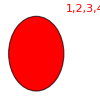
-Graphics-{14348906→v123456,1/6}

```mathematica
CosyPrint6[14348906]
```

```mathematica
shortKeys=Monitor[Select[Keys[stubbornForm6],(xyz=#;Length[stubbornForm6[#,"colofour2"]]==0)&],xyz];
```

```mathematica
Length[shortKeys]
```

1

```mathematica
shortKeys
```

{14348906}

```mathematica
repP=Monitor[Table[stubbornForm6[k,"colofour"]->Style[stubbornForm6[k,"colofour2"], If[ToString[stubbornForm6[k,"comp"]]=="GreaterEqual",Red,Green]],{k,baseKeys6}],k];Length[repP]
```

203

```mathematica
Take[repP,3]
```

{v123456→p1x2x3x4x5x6,v12345x6→p16x2x3x4x5+p1x26x3x4x5+p1x2x36x4x5+p1x2x3x46x5+p1x2x3x4x56+p1x2x3x4x5x6,v12346x5→p15x2x3x4x6+p1x25x3x4x6+p1x2x35x4x6+p1x2x3x45x6+p1x2x3x4x56+p1x2x3x4x5x6}

```mathematica
stubbornForm6[1,"colofour"]
```

v12345x6+v12346x5+v1234x5x6+v1235x46+v1235x4x6+v1236x45+v1236x4x5+v123x45x6+v123x46x5+v123x4x5x6+v1245x36+v1245x3x6+v1246x35+v1246x3x5+v124x35x6+v124x36x5+v124x3x5x6+v125x346+v125x34x6+v125x36x4+v125x3x46+v125x3x4x6+v126x345+v126x34x5+v126x35x4+v126x3x45+v126x3x4x5+v12x345x6+v12x346x5+v12x34x5x6+v12x35x46+v12x35x4x6+v12x36x45+v12x36x4x5+v12x3x45x6+v12x3x46x5+v12x3x4x5x6+v1345x26+v1345x2x6+v1346x25+v1346x2x5+v134x25x6+v134x26x5+v134x2x5x6+v135x246+v135x24x6+v135x26x4+v135x2x46+v135x2x4x6+v136x245+v136x24x5+v136x25x4+v136x2x45+v136x2x4x5+v13x245x6+v13x246x5+v13x24x5x6+v13x25x46+v13x25x4x6+v13x26x45+v13x26x4x5+v13x2x45x6+v13x2x46x5+v13x2x4x5x6+v145x236+v145x23x6+v145x26x3+v145x2x36+v145x2x3x6+v146x235+v146x23x5+v146x25x3+v146x2x35+v146x2x3x5+v14x235x6+v14x236x5+v14x23x5x6+v14x25x36+v14x25x3x6+v14x26x35+v14x26x3x5+v14x2x35x6+v14x2x36x5+v14x2x3x5x6+v15x2346+v15x234x6+v15x236x4+v15x23x46+v15x23x4x6+v15x246x3+v15x24x36+v15x24x3x6+v15x26x34+v15x26x3x4+v15x2x346+v15x2x34x6+v15x2x36x4+v15x2x3x46+v15x2x3x4x6+v16x2345+v16x234x5+v16x235x4+v16x23x45+v16x23x4x5+v16x245x3+v16x24x35+v16x24x3x5+v16x25x34+v16x25x3x4+v16x2x345+v16x2x34x5+v16x2x35x4+v16x2x3x45+v16x2x3x4x5+v1x2345x6+v1x2346x5+v1x234x5x6+v1x235x46+v1x235x4x6+v1x236x45+v1x236x4x5+v1x23x45x6+v1x23x46x5+v1x23x4x5x6+v1x245x36+v1x245x3x6+v1x246x35+v1x246x3x5+v1x24x35x6+v1x24x36x5+v1x24x3x5x6+v1x25x346+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x26x345+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x345x6+v1x2x346x5+v1x2x34x5x6+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x5x6

```mathematica
stubbornForm6[1,"colofour2"]
```

p123456+5 p12345x6+5 p12346x5+21 p1234x56+21 p1234x5x6+6 p12356x4+17 p1235x46+21 p1235x4x6+17 p1236x45+21 p1236x4x5+34 p123x456+47 p123x45x6+47 p123x46x5+60 p123x4x56+60 p123x4x5x6+6 p12456x3+17 p1245x36+21 p1245x3x6+17 p1246x35+21 p1246x3x5+34 p124x356+47 p124x35x6+47 p124x36x5+60 p124x3x56+60 p124x3x5x6+21 p1256x34+26 p1256x3x4+27 p125x346+47 p125x34x6+47 p125x36x4+47 p125x3x46+60 p125x3x4x6+27 p126x345+47 p126x34x5+47 p126x35x4+47 p126x3x45+60 p126x3x4x5+21 p12x3456+47 p12x345x6+47 p12x346x5+87 p12x34x56+87 p12x34x5x6+60 p12x356x4+67 p12x35x46+87 p12x35x4x6+67 p12x36x45+87 p12x36x4x5+60 p12x3x456+87 p12x3x45x6+87 p12x3x46x5+114 p12x3x4x56+114 p12x3x4x5x6+6 p13456x2+17 p1345x26+21 p1345x2x6+17 p1346x25+21 p1346x2x5+34 p134x256+47 p134x25x6+47 p134x26x5+60 p134x2x56+60 p134x2x5x6+21 p1356x24+26 p1356x2x4+27 p135x246+47 p135x24x6+47 p135x26x4+47 p135x2x46+60 p135x2x4x6+27 p136x245+47 p136x24x5+47 p136x25x4+47 p136x2x45+60 p136x2x4x5+21 p13x2456+47 p13x245x6+47 p13x246x5+87 p13x24x56+87 p13x24x5x6+60 p13x256x4+67 p13x25x46+87 p13x25x4x6+67 p13x26x45+87 p13x26x4x5+60 p13x2x456+87 p13x2x45x6+87 p13x2x46x5+114 p13x2x4x56+114 p13x2x4x5x6+21 p1456x23+26 p1456x2x3+27 p145x236+47 p145x23x6+47 p145x26x3+47 p145x2x36+60 p145x2x3x6+27 p146x235+47 p146x23x5+47 p146x25x3+47 p146x2x35+60 p146x2x3x5+21 p14x2356+47 p14x235x6+47 p14x236x5+87 p14x23x56+87 p14x23x5x6+60 p14x256x3+67 p14x25x36+87 p14x25x3x6+67 p14x26x35+87 p14x26x3x5+60 p14x2x356+87 p14x2x35x6+87 p14x2x36x5+114 p14x2x3x56+114 p14x2x3x5x6+34 p156x234+60 p156x23x4+60 p156x24x3+60 p156x2x34+77 p156x2x3x4+17 p15x2346+47 p15x234x6+47 p15x236x4+67 p15x23x46+87 p15x23x4x6+47 p15x246x3+67 p15x24x36+87 p15x24x3x6+67 p15x26x34+87 p15x26x3x4+47 p15x2x346+87 p15x2x34x6+87 p15x2x36x4+87 p15x2x3x46+114 p15x2x3x4x6+17 p16x2345+47 p16x234x5+47 p16x235x4+67 p16x23x45+87 p16x23x4x5+47 p16x245x3+67 p16x24x35+87 p16x24x3x5+67 p16x25x34+87 p16x25x3x4+47 p16x2x345+87 p16x2x34x5+87 p16x2x35x4+87 p16x2x3x45+114 p16x2x3x4x5+6 p1x23456+21 p1x2345x6+21 p1x2346x5+60 p1x234x56+60 p1x234x5x6+26 p1x2356x4+47 p1x235x46+60 p1x235x4x6+47 p1x236x45+60 p1x236x4x5+60 p1x23x456+87 p1x23x45x6+87 p1x23x46x5+114 p1x23x4x56+114 p1x23x4x5x6+26 p1x2456x3+47 p1x245x36+60 p1x245x3x6+47 p1x246x35+60 p1x246x3x5+60 p1x24x356+87 p1x24x35x6+87 p1x24x36x5+114 p1x24x3x56+114 p1x24x3x5x6+60 p1x256x34+77 p1x256x3x4+47 p1x25x346+87 p1x25x34x6+87 p1x25x36x4+87 p1x25x3x46+114 p1x25x3x4x6+47 p1x26x345+87 p1x26x34x5+87 p1x26x35x4+87 p1x26x3x45+114 p1x26x3x4x5+26 p1x2x3456+60 p1x2x345x6+60 p1x2x346x5+114 p1x2x34x56+114 p1x2x34x5x6+77 p1x2x356x4+87 p1x2x35x46+114 p1x2x35x4x6+87 p1x2x36x45+114 p1x2x36x4x5+77 p1x2x3x456+114 p1x2x3x45x6+114 p1x2x3x46x5+151 p1x2x3x4x56+151 p1x2x3x4x5x6

```mathematica
newKeys=Select[Keys[stubbornForm6],Length[ListofVars[stubbornForm6[#,"colofour2"]]]==1&];Length[newKeys]
```

1

```mathematica
Table[stubbornForm6[k,"colofour2"]->stubbornForm6[k,"graph"],{k,newKeys}];
```

```mathematica
grapRep=Table[stubbornForm6[k,"colofour2"]->stubbornForm6[k,"graph"],{k,newKeys}];
```

```mathematica
Eigenvalues[mat62]
```

```mathematica
Tr[Inverse[mat6]]
```

1

```mathematica
Map[Total[#]&,mat6]//Tally//Sort
```

{{0,202},{1,1}}

```mathematica
Map[Total[#]&,mat62]//Tally//Sort
```

{{1,1},{6,6},{21,15},{26,15},{34,10},{60,60},{77,20},{87,15},{114,45},{151,15},{203,1}}

```mathematica
MatrixForm[mat62]
```

```mathematica
GenerateRep[assoc_, vertexCount_]:=Block[
{keysWith6Nodes=Select[Keys[assoc],With[{g=assoc[#]["graph"]},VertexCount[g]==vertexCount]&],
allPartitions=SetPartitions[vertexCount]},
Monitor[ 
Table[
With[
{key=First[Select[keysWith6Nodes,With[{g=assoc[#]["graph"]},IsPartitionGraph[g,part]]&]]},
assoc[key,"colofour2"]->Style[assoc[key,"colofour2"], If[ToString[assoc[key,"comp"]]=="GreaterEqual",Red,Green]]
],
{part,allPartitions}],part]
]
```

```mathematica
repP = GenerateRep[stubbornForm6, 6];Take[repP,5]
```

{p123456+p12345x6+p12346x5+p1234x56+p1234x5x6+p12356x4+p1235x46+p1235x4x6+p1236x45+p1236x4x5+p123x456+p123x45x6+p123x46x5+p123x4x56+p123x4x5x6+p12456x3+p1245x36+p1245x3x6+p1246x35+p1246x3x5+p124x356+p124x35x6+p124x36x5+p124x3x56+p124x3x5x6+p1256x34+p1256x3x4+p125x346+p125x34x6+p125x36x4+p125x3x46+p125x3x4x6+p126x345+p126x34x5+p126x35x4+p126x3x45+p126x3x4x5+p12x3456+p12x345x6+p12x346x5+p12x34x56+p12x34x5x6+p12x356x4+p12x35x46+p12x35x4x6+p12x36x45+p12x36x4x5+p12x3x456+p12x3x45x6+p12x3x46x5+p12x3x4x56+p12x3x4x5x6+p13456x2+p1345x26+p1345x2x6+p1346x25+p1346x2x5+p134x256+p134x25x6+p134x26x5+p134x2x56+p134x2x5x6+p1356x24+p1356x2x4+p135x246+p135x24x6+p135x26x4+p135x2x46+p135x2x4x6+p136x245+p136x24x5+p136x25x4+p136x2x45+p136x2x4x5+p13x2456+p13x245x6+p13x246x5+p13x24x56+p13x24x5x6+p13x256x4+p13x25x46+p13x25x4x6+p13x26x45+p13x26x4x5+p13x2x456+p13x2x45x6+p13x2x46x5+p13x2x4x56+p13x2x4x5x6+p1456x23+p1456x2x3+p145x236+p145x23x6+p145x26x3+p145x2x36+p145x2x3x6+p146x235+p146x23x5+p146x25x3+p146x2x35+p146x2x3x5+p14x2356+p14x235x6+p14x236x5+p14x23x56+p14x23x5x6+p14x256x3+p14x25x36+p14x25x3x6+p14x26x35+p14x26x3x5+p14x2x356+p14x2x35x6+p14x2x36x5+p14x2x3x56+p14x2x3x5x6+p156x234+p156x23x4+p156x24x3+p156x2x34+p156x2x3x4+p15x2346+p15x234x6+p15x236x4+p15x23x46+p15x23x4x6+p15x246x3+p15x24x36+p15x24x3x6+p15x26x34+p15x26x3x4+p15x2x346+p15x2x34x6+p15x2x36x4+p15x2x3x46+p15x2x3x4x6+p16x2345+p16x234x5+p16x235x4+p16x23x45+p16x23x4x5+p16x245x3+p16x24x35+p16x24x3x5+p16x25x34+p16x25x3x4+p16x2x345+p16x2x34x5+p16x2x35x4+p16x2x3x45+p16x2x3x4x5+p1x23456+p1x2345x6+p1x2346x5+p1x234x56+p1x234x5x6+p1x2356x4+p1x235x46+p1x235x4x6+p1x236x45+p1x236x4x5+p1x23x456+p1x23x45x6+p1x23x46x5+p1x23x4x56+p1x23x4x5x6+p1x2456x3+p1x245x36+p1x245x3x6+p1x246x35+p1x246x3x5+p1x24x356+p1x24x35x6+p1x24x36x5+p1x24x3x56+p1x24x3x5x6+p1x256x34+p1x256x3x4+p1x25x346+p1x25x34x6+p1x25x36x4+p1x25x3x46+p1x25x3x4x6+p1x26x345+p1x26x34x5+p1x26x35x4+p1x26x3x45+p1x26x3x4x5+p1x2x3456+p1x2x345x6+p1x2x346x5+p1x2x34x56+p1x2x34x5x6+p1x2x356x4+p1x2x35x46+p1x2x35x4x6+p1x2x36x45+p1x2x36x4x5+p1x2x3x456+p1x2x3x45x6+p1x2x3x46x5+p1x2x3x4x56+p1x2x3x4x5x6→p123456+p12345x6+p12346x5+p1234x56+p1234x5x6+p12356x4+p1235x46+p1235x4x6+p1236x45+p1236x4x5+p123x456+p123x45x6+p123x46x5+p123x4x56+p123x4x5x6+p12456x3+p1245x36+p1245x3x6+p1246x35+p1246x3x5+p124x356+p124x35x6+p124x36x5+p124x3x56+p124x3x5x6+p1256x34+p1256x3x4+p125x346+p125x34x6+p125x36x4+p125x3x46+p125x3x4x6+p126x345+p126x34x5+p126x35x4+p126x3x45+p126x3x4x5+p12x3456+p12x345x6+p12x346x5+p12x34x56+p12x34x5x6+p12x356x4+p12x35x46+p12x35x4x6+p12x36x45+p12x36x4x5+p12x3x456+p12x3x45x6+p12x3x46x5+p12x3x4x56+p12x3x4x5x6+p13456x2+p1345x26+p1345x2x6+p1346x25+p1346x2x5+p134x256+p134x25x6+p134x26x5+p134x2x56+p134x2x5x6+p1356x24+p1356x2x4+p135x246+p135x24x6+p135x26x4+p135x2x46+p135x2x4x6+p136x245+p136x24x5+p136x25x4+p136x2x45+p136x2x4x5+p13x2456+p13x245x6+p13x246x5+p13x24x56+p13x24x5x6+p13x256x4+p13x25x46+p13x25x4x6+p13x26x45+p13x26x4x5+p13x2x456+p13x2x45x6+p13x2x46x5+p13x2x4x56+p13x2x4x5x6+p1456x23+p1456x2x3+p145x236+p145x23x6+p145x26x3+p145x2x36+p145x2x3x6+p146x235+p146x23x5+p146x25x3+p146x2x35+p146x2x3x5+p14x2356+p14x235x6+p14x236x5+p14x23x56+p14x23x5x6+p14x256x3+p14x25x36+p14x25x3x6+p14x26x35+p14x26x3x5+p14x2x356+p14x2x35x6+p14x2x36x5+p14x2x3x56+p14x2x3x5x6+p156x234+p156x23x4+p156x24x3+p156x2x34+p156x2x3x4+p15x2346+p15x234x6+p15x236x4+p15x23x46+p15x23x4x6+p15x246x3+p15x24x36+p15x24x3x6+p15x26x34+p15x26x3x4+p15x2x346+p15x2x34x6+p15x2x36x4+p15x2x3x46+p15x2x3x4x6+p16x2345+p16x234x5+p16x235x4+p16x23x45+p16x23x4x5+p16x245x3+p16x24x35+p16x24x3x5+p16x25x34+p16x25x3x4+p16x2x345+p16x2x34x5+p16x2x35x4+p16x2x3x45+p16x2x3x4x5+p1x23456+p1x2345x6+p1x2346x5+p1x234x56+p1x234x5x6+p1x2356x4+p1x235x46+p1x235x4x6+p1x236x45+p1x236x4x5+p1x23x456+p1x23x45x6+p1x23x46x5+p1x23x4x56+p1x23x4x5x6+p1x2456x3+p1x245x36+p1x245x3x6+p1x246x35+p1x246x3x5+p1x24x356+p1x24x35x6+p1x24x36x5+p1x24x3x56+p1x24x3x5x6+p1x256x34+p1x256x3x4+p1x25x346+p1x25x34x6+p1x25x36x4+p1x25x3x46+p1x25x3x4x6+p1x26x345+p1x26x34x5+p1x26x35x4+p1x26x3x45+p1x26x3x4x5+p1x2x3456+p1x2x345x6+p1x2x346x5+p1x2x34x56+p1x2x34x5x6+p1x2x356x4+p1x2x35x46+p1x2x35x4x6+p1x2x36x45+p1x2x36x4x5+p1x2x3x456+p1x2x3x45x6+p1x2x3x46x5+p1x2x3x4x56+p1x2x3x4x5x6,p123456+2 p12345x6+2 p12346x5+3 p1234x56+3 p1234x5x6+2 p12356x4+3 p1235x46+3 p1235x4x6+3 p1236x45+3 p1236x4x5+4 p123x456+4 p123x45x6+4 p123x46x5+4 p123x4x56+4 p123x4x5x6+2 p12456x3+3 p1245x36+3 p1245x3x6+3 p1246x35+3 p1246x3x5+4 p124x356+4 p124x35x6+4 p124x36x5+4 p124x3x56+4 p124x3x5x6+3 p1256x34+3 p1256x3x4+4 p125x346+4 p125x34x6+4 p125x36x4+4 p125x3x46+4 p125x3x4x6+4 p126x345+4 p126x34x5+4 p126x35x4+4 p126x3x45+4 p126x3x4x5+5 p12x3456+5 p12x345x6+5 p12x346x5+5 p12x34x56+5 p12x34x5x6+5 p12x356x4+5 p12x35x46+5 p12x35x4x6+5 p12x36x45+5 p12x36x4x5+5 p12x3x456+5 p12x3x45x6+5 p12x3x46x5+5 p12x3x4x56+5 p12x3x4x5x6+2 p13456x2+3 p1345x26+3 p1345x2x6+3 p1346x25+3 p1346x2x5+4 p134x256+4 p134x25x6+4 p134x26x5+4 p134x2x56+4 p134x2x5x6+3 p1356x24+3 p1356x2x4+4 p135x246+4 p135x24x6+4 p135x26x4+4 p135x2x46+4 p135x2x4x6+4 p136x245+4 p136x24x5+4 p136x25x4+4 p136x2x45+4 p136x2x4x5+5 p13x2456+5 p13x245x6+5 p13x246x5+5 p13x24x56+5 p13x24x5x6+5 p13x256x4+5 p13x25x46+5 p13x25x4x6+5 p13x26x45+5 p13x26x4x5+5 p13x2x456+5 p13x2x45x6+5 p13x2x46x5+5 p13x2x4x56+5 p13x2x4x5x6+3 p1456x23+3 p1456x2x3+4 p145x236+4 p145x23x6+4 p145x26x3+4 p145x2x36+4 p145x2x3x6+4 p146x235+4 p146x23x5+4 p146x25x3+4 p146x2x35+4 p146x2x3x5+5 p14x2356+5 p14x235x6+5 p14x236x5+5 p14x23x56+5 p14x23x5x6+5 p14x256x3+5 p14x25x36+5 p14x25x3x6+5 p14x26x35+5 p14x26x3x5+5 p14x2x356+5 p14x2x35x6+5 p14x2x36x5+5 p14x2x3x56+5 p14x2x3x5x6+4 p156x234+4 p156x23x4+4 p156x24x3+4 p156x2x34+4 p156x2x3x4+5 p15x2346+5 p15x234x6+5 p15x236x4+5 p15x23x46+5 p15x23x4x6+5 p15x246x3+5 p15x24x36+5 p15x24x3x6+5 p15x26x34+5 p15x26x3x4+5 p15x2x346+5 p15x2x34x6+5 p15x2x36x4+5 p15x2x3x46+5 p15x2x3x4x6+5 p16x2345+5 p16x234x5+5 p16x235x4+5 p16x23x45+5 p16x23x4x5+5 p16x245x3+5 p16x24x35+5 p16x24x3x5+5 p16x25x34+5 p16x25x3x4+5 p16x2x345+5 p16x2x34x5+5 p16x2x35x4+5 p16x2x3x45+5 p16x2x3x4x5+6 p1x23456+6 p1x2345x6+6 p1x2346x5+6 p1x234x56+6 p1x234x5x6+6 p1x2356x4+6 p1x235x46+6 p1x235x4x6+6 p1x236x45+6 p1x236x4x5+6 p1x23x456+6 p1x23x45x6+6 p1x23x46x5+6 p1x23x4x56+6 p1x23x4x5x6+6 p1x2456x3+6 p1x245x36+6 p1x245x3x6+6 p1x246x35+6 p1x246x3x5+6 p1x24x356+6 p1x24x35x6+6 p1x24x36x5+6 p1x24x3x56+6 p1x24x3x5x6+6 p1x256x34+6 p1x256x3x4+6 p1x25x346+6 p1x25x34x6+6 p1x25x36x4+6 p1x25x3x46+6 p1x25x3x4x6+6 p1x26x345+6 p1x26x34x5+6 p1x26x35x4+6 p1x26x3x45+6 p1x26x3x4x5+6 p1x2x3456+6 p1x2x345x6+6 p1x2x346x5+6 p1x2x34x56+6 p1x2x34x5x6+6 p1x2x356x4+6 p1x2x35x46+6 p1x2x35x4x6+6 p1x2x36x45+6 p1x2x36x4x5+6 p1x2x3x456+6 p1x2x3x45x6+6 p1x2x3x46x5+6 p1x2x3x4x56+6 p1x2x3x4x5x6→p123456+2 p12345x6+2 p12346x5+3 p1234x56+3 p1234x5x6+2 p12356x4+3 p1235x46+3 p1235x4x6+3 p1236x45+3 p1236x4x5+4 p123x456+4 p123x45x6+4 p123x46x5+4 p123x4x56+4 p123x4x5x6+2 p12456x3+3 p1245x36+3 p1245x3x6+3 p1246x35+3 p1246x3x5+4 p124x356+4 p124x35x6+4 p124x36x5+4 p124x3x56+4 p124x3x5x6+3 p1256x34+3 p1256x3x4+4 p125x346+4 p125x34x6+4 p125x36x4+4 p125x3x46+4 p125x3x4x6+4 p126x345+4 p126x34x5+4 p126x35x4+4 p126x3x45+4 p126x3x4x5+5 p12x3456+5 p12x345x6+5 p12x346x5+5 p12x34x56+5 p12x34x5x6+5 p12x356x4+5 p12x35x46+5 p12x35x4x6+5 p12x36x45+5 p12x36x4x5+5 p12x3x456+5 p12x3x45x6+5 p12x3x46x5+5 p12x3x4x56+5 p12x3x4x5x6+2 p13456x2+3 p1345x26+3 p1345x2x6+3 p1346x25+3 p1346x2x5+4 p134x256+4 p134x25x6+4 p134x26x5+4 p134x2x56+4 p134x2x5x6+3 p1356x24+3 p1356x2x4+4 p135x246+4 p135x24x6+4 p135x26x4+4 p135x2x46+4 p135x2x4x6+4 p136x245+4 p136x24x5+4 p136x25x4+4 p136x2x45+4 p136x2x4x5+5 p13x2456+5 p13x245x6+5 p13x246x5+5 p13x24x56+5 p13x24x5x6+5 p13x256x4+5 p13x25x46+5 p13x25x4x6+5 p13x26x45+5 p13x26x4x5+5 p13x2x456+5 p13x2x45x6+5 p13x2x46x5+5 p13x2x4x56+5 p13x2x4x5x6+3 p1456x23+3 p1456x2x3+4 p145x236+4 p145x23x6+4 p145x26x3+4 p145x2x36+4 p145x2x3x6+4 p146x235+4 p146x23x5+4 p146x25x3+4 p146x2x35+4 p146x2x3x5+5 p14x2356+5 p14x235x6+5 p14x236x5+5 p14x23x56+5 p14x23x5x6+5 p14x256x3+5 p14x25x36+5 p14x25x3x6+5 p14x26x35+5 p14x26x3x5+5 p14x2x356+5 p14x2x35x6+5 p14x2x36x5+5 p14x2x3x56+5 p14x2x3x5x6+4 p156x234+4 p156x23x4+4 p156x24x3+4 p156x2x34+4 p156x2x3x4+5 p15x2346+5 p15x234x6+5 p15x236x4+5 p15x23x46+5 p15x23x4x6+5 p15x246x3+5 p15x24x36+5 p15x24x3x6+5 p15x26x34+5 p15x26x3x4+5 p15x2x346+5 p15x2x34x6+5 p15x2x36x4+5 p15x2x3x46+5 p15x2x3x4x6+5 p16x2345+5 p16x234x5+5 p16x235x4+5 p16x23x45+5 p16x23x4x5+5 p16x245x3+5 p16x24x35+5 p16x24x3x5+5 p16x25x34+5 p16x25x3x4+5 p16x2x345+5 p16x2x34x5+5 p16x2x35x4+5 p16x2x3x45+5 p16x2x3x4x5+6 p1x23456+6 p1x2345x6+6 p1x2346x5+6 p1x234x56+6 p1x234x5x6+6 p1x2356x4+6 p1x235x46+6 p1x235x4x6+6 p1x236x45+6 p1x236x4x5+6 p1x23x456+6 p1x23x45x6+6 p1x23x46x5+6 p1x23x4x56+6 p1x23x4x5x6+6 p1x2456x3+6 p1x245x36+6 p1x245x3x6+6 p1x246x35+6 p1x246x3x5+6 p1x24x356+6 p1x24x35x6+6 p1x24x36x5+6 p1x24x3x56+6 p1x24x3x5x6+6 p1x256x34+6 p1x256x3x4+6 p1x25x346+6 p1x25x34x6+6 p1x25x36x4+6 p1x25x3x46+6 p1x25x3x4x6+6 p1x26x345+6 p1x26x34x5+6 p1x26x35x4+6 p1x26x3x45+6 p1x26x3x4x5+6 p1x2x3456+6 p1x2x345x6+6 p1x2x346x5+6 p1x2x34x56+6 p1x2x34x5x6+6 p1x2x356x4+6 p1x2x35x46+6 p1x2x35x4x6+6 p1x2x36x45+6 p1x2x36x4x5+6 p1x2x3x456+6 p1x2x3x45x6+6 p1x2x3x46x5+6 p1x2x3x4x56+6 p1x2x3x4x5x6,p123456+3 p12345x6+3 p12346x5+7 p1234x56+7 p1234x5x6+3 p12356x4+7 p1235x46+7 p1235x4x6+7 p1236x45+7 p1236x4x5+13 p123x456+13 p123x45x6+13 p123x46x5+13 p123x4x56+13 p123x4x5x6+3 p12456x3+7 p1245x36+7 p1245x3x6+7 p1246x35+7 p1246x3x5+13 p124x356+13 p124x35x6+13 p124x36x5+13 p124x3x56+13 p124x3x5x6+7 p1256x34+7 p1256x3x4+13 p125x346+13 p125x34x6+13 p125x36x4+13 p125x3x46+13 p125x3x4x6+13 p126x345+13 p126x34x5+13 p126x35x4+13 p126x3x45+13 p126x3x4x5+21 p12x3456+21 p12x345x6+21 p12x346x5+21 p12x34x56+21 p12x34x5x6+21 p12x356x4+21 p12x35x46+21 p12x35x4x6+21 p12x36x45+21 p12x36x4x5+21 p12x3x456+21 p12x3x45x6+21 p12x3x46x5+21 p12x3x4x56+21 p12x3x4x5x6+5 p13456x2+8 p1345x26+9 p1345x2x6+8 p1346x25+9 p1346x2x5+9 p134x256+11 p134x25x6+11 p134x26x5+13 p134x2x56+13 p134x2x5x6+8 p1356x24+9 p1356x2x4+9 p135x246+11 p135x24x6+11 p135x26x4+13 p135x2x46+13 p135x2x4x6+9 p136x245+11 p136x24x5+11 p136x25x4+13 p136x2x45+13 p136x2x4x5+8 p13x2456+11 p13x245x6+11 p13x246x5+14 p13x24x56+14 p13x24x5x6+11 p13x256x4+14 p13x25x46+14 p13x25x4x6+14 p13x26x45+14 p13x26x4x5+17 p13x2x456+17 p13x2x45x6+17 p13x2x46x5+17 p13x2x4x56+17 p13x2x4x5x6+8 p1456x23+9 p1456x2x3+9 p145x236+11 p145x23x6+11 p145x26x3+13 p145x2x36+13 p145x2x3x6+9 p146x235+11 p146x23x5+11 p146x25x3+13 p146x2x35+13 p146x2x3x5+8 p14x2356+11 p14x235x6+11 p14x236x5+14 p14x23x56+14 p14x23x5x6+11 p14x256x3+14 p14x25x36+14 p14x25x3x6+14 p14x26x35+14 p14x26x3x5+17 p14x2x356+17 p14x2x35x6+17 p14x2x36x5+17 p14x2x3x56+17 p14x2x3x5x6+9 p156x234+11 p156x23x4+11 p156x24x3+13 p156x2x34+13 p156x2x3x4+8 p15x2346+11 p15x234x6+11 p15x236x4+14 p15x23x46+14 p15x23x4x6+11 p15x246x3+14 p15x24x36+14 p15x24x3x6+14 p15x26x34+14 p15x26x3x4+17 p15x2x346+17 p15x2x34x6+17 p15x2x36x4+17 p15x2x3x46+17 p15x2x3x4x6+8 p16x2345+11 p16x234x5+11 p16x235x4+14 p16x23x45+14 p16x23x4x5+11 p16x245x3+14 p16x24x35+14 p16x24x3x5+14 p16x25x34+14 p16x25x3x4+17 p16x2x345+17 p16x2x34x5+17 p16x2x35x4+17 p16x2x3x45+17 p16x2x3x4x5+5 p1x23456+9 p1x2345x6+9 p1x2346x5+13 p1x234x56+13 p1x234x5x6+9 p1x2356x4+13 p1x235x46+13 p1x235x4x6+13 p1x236x45+13 p1x236x4x5+17 p1x23x456+17 p1x23x45x6+17 p1x23x46x5+17 p1x23x4x56+17 p1x23x4x5x6+9 p1x2456x3+13 p1x245x36+13 p1x245x3x6+13 p1x246x35+13 p1x246x3x5+17 p1x24x356+17 p1x24x35x6+17 p1x24x36x5+17 p1x24x3x56+17 p1x24x3x5x6+13 p1x256x34+13 p1x256x3x4+17 p1x25x346+17 p1x25x34x6+17 p1x25x36x4+17 p1x25x3x46+17 p1x25x3x4x6+17 p1x26x345+17 p1x26x34x5+17 p1x26x35x4+17 p1x26x3x45+17 p1x26x3x4x5+21 p1x2x3456+21 p1x2x345x6+21 p1x2x346x5+21 p1x2x34x56+21 p1x2x34x5x6+21 p1x2x356x4+21 p1x2x35x46+21 p1x2x35x4x6+21 p1x2x36x45+21 p1x2x36x4x5+21 p1x2x3x456+21 p1x2x3x45x6+21 p1x2x3x46x5+21 p1x2x3x4x56+21 p1x2x3x4x5x6→p123456+3 p12345x6+3 p12346x5+7 p1234x56+7 p1234x5x6+3 p12356x4+7 p1235x46+7 p1235x4x6+7 p1236x45+7 p1236x4x5+13 p123x456+13 p123x45x6+13 p123x46x5+13 p123x4x56+13 p123x4x5x6+3 p12456x3+7 p1245x36+7 p1245x3x6+7 p1246x35+7 p1246x3x5+13 p124x356+13 p124x35x6+13 p124x36x5+13 p124x3x56+13 p124x3x5x6+7 p1256x34+7 p1256x3x4+13 p125x346+13 p125x34x6+13 p125x36x4+13 p125x3x46+13 p125x3x4x6+13 p126x345+13 p126x34x5+13 p126x35x4+13 p126x3x45+13 p126x3x4x5+21 p12x3456+21 p12x345x6+21 p12x346x5+21 p12x34x56+21 p12x34x5x6+21 p12x356x4+21 p12x35x46+21 p12x35x4x6+21 p12x36x45+21 p12x36x4x5+21 p12x3x456+21 p12x3x45x6+21 p12x3x46x5+21 p12x3x4x56+21 p12x3x4x5x6+5 p13456x2+8 p1345x26+9 p1345x2x6+8 p1346x25+9 p1346x2x5+9 p134x256+11 p134x25x6+11 p134x26x5+13 p134x2x56+13 p134x2x5x6+8 p1356x24+9 p1356x2x4+9 p135x246+11 p135x24x6+11 p135x26x4+13 p135x2x46+13 p135x2x4x6+9 p136x245+11 p136x24x5+11 p136x25x4+13 p136x2x45+13 p136x2x4x5+8 p13x2456+11 p13x245x6+11 p13x246x5+14 p13x24x56+14 p13x24x5x6+11 p13x256x4+14 p13x25x46+14 p13x25x4x6+14 p13x26x45+14 p13x26x4x5+17 p13x2x456+17 p13x2x45x6+17 p13x2x46x5+17 p13x2x4x56+17 p13x2x4x5x6+8 p1456x23+9 p1456x2x3+9 p145x236+11 p145x23x6+11 p145x26x3+13 p145x2x36+13 p145x2x3x6+9 p146x235+11 p146x23x5+11 p146x25x3+13 p146x2x35+13 p146x2x3x5+8 p14x2356+11 p14x235x6+11 p14x236x5+14 p14x23x56+14 p14x23x5x6+11 p14x256x3+14 p14x25x36+14 p14x25x3x6+14 p14x26x35+14 p14x26x3x5+17 p14x2x356+17 p14x2x35x6+17 p14x2x36x5+17 p14x2x3x56+17 p14x2x3x5x6+9 p156x234+11 p156x23x4+11 p156x24x3+13 p156x2x34+13 p156x2x3x4+8 p15x2346+11 p15x234x6+11 p15x236x4+14 p15x23x46+14 p15x23x4x6+11 p15x246x3+14 p15x24x36+14 p15x24x3x6+14 p15x26x34+14 p15x26x3x4+17 p15x2x346+17 p15x2x34x6+17 p15x2x36x4+17 p15x2x3x46+17 p15x2x3x4x6+8 p16x2345+11 p16x234x5+11 p16x235x4+14 p16x23x45+14 p16x23x4x5+11 p16x245x3+14 p16x24x35+14 p16x24x3x5+14 p16x25x34+14 p16x25x3x4+17 p16x2x345+17 p16x2x34x5+17 p16x2x35x4+17 p16x2x3x45+17 p16x2x3x4x5+5 p1x23456+9 p1x2345x6+9 p1x2346x5+13 p1x234x56+13 p1x234x5x6+9 p1x2356x4+13 p1x235x46+13 p1x235x4x6+13 p1x236x45+13 p1x236x4x5+17 p1x23x456+17 p1x23x45x6+17 p1x23x46x5+17 p1x23x4x56+17 p1x23x4x5x6+9 p1x2456x3+13 p1x245x36+13 p1x245x3x6+13 p1x246x35+13 p1x246x3x5+17 p1x24x356+17 p1x24x35x6+17 p1x24x36x5+17 p1x24x3x56+17 p1x24x3x5x6+13 p1x256x34+13 p1x256x3x4+17 p1x25x346+17 p1x25x34x6+17 p1x25x36x4+17 p1x25x3x46+17 p1x25x3x4x6+17 p1x26x345+17 p1x26x34x5+17 p1x26x35x4+17 p1x26x3x45+17 p1x26x3x4x5+21 p1x2x3456+21 p1x2x345x6+21 p1x2x346x5+21 p1x2x34x56+21 p1x2x34x5x6+21 p1x2x356x4+21 p1x2x35x46+21 p1x2x35x4x6+21 p1x2x36x45+21 p1x2x36x4x5+21 p1x2x3x456+21 p1x2x3x45x6+21 p1x2x3x46x5+21 p1x2x3x4x56+21 p1x2x3x4x5x6,p123456+2 p12345x6+2 p12346x5+3 p1234x56+3 p1234x5x6+2 p12356x4+3 p1235x46+3 p1235x4x6+3 p1236x45+3 p1236x4x5+4 p123x456+4 p123x45x6+4 p123x46x5+4 p123x4x56+4 p123x4x5x6+2 p12456x3+3 p1245x36+3 p1245x3x6+3 p1246x35+3 p1246x3x5+4 p124x356+4 p124x35x6+4 p124x36x5+4 p124x3x56+4 p124x3x5x6+3 p1256x34+3 p1256x3x4+4 p125x346+4 p125x34x6+4 p125x36x4+4 p125x3x46+4 p125x3x4x6+4 p126x345+4 p126x34x5+4 p126x35x4+4 p126x3x45+4 p126x3x4x5+5 p12x3456+5 p12x345x6+5 p12x346x5+5 p12x34x56+5 p12x34x5x6+5 p12x356x4+5 p12x35x46+5 p12x35x4x6+5 p12x36x45+5 p12x36x4x5+5 p12x3x456+5 p12x3x45x6+5 p12x3x46x5+5 p12x3x4x56+5 p12x3x4x5x6+6 p13456x2+5 p1345x26+6 p1345x2x6+5 p1346x25+6 p1346x2x5+4 p134x256+5 p134x25x6+5 p134x26x5+6 p134x2x56+6 p134x2x5x6+5 p1356x24+6 p1356x2x4+4 p135x246+5 p135x24x6+5 p135x26x4+6 p135x2x46+6 p135x2x4x6+4 p136x245+5 p136x24x5+5 p136x25x4+6 p136x2x45+6 p136x2x4x5+3 p13x2456+4 p13x245x6+4 p13x246x5+5 p13x24x56+5 p13x24x5x6+4 p13x256x4+5 p13x25x46+5 p13x25x4x6+5 p13x26x45+5 p13x26x4x5+6 p13x2x456+6 p13x2x45x6+6 p13x2x46x5+6 p13x2x4x56+6 p13x2x4x5x6+5 p1456x23+6 p1456x2x3+4 p145x236+5 p145x23x6+5 p145x26x3+6 p145x2x36+6 p145x2x3x6+4 p146x235+5 p146x23x5+5 p146x25x3+6 p146x2x35+6 p146x2x3x5+3 p14x2356+4 p14x235x6+4 p14x236x5+5 p14x23x56+5 p14x23x5x6+4 p14x256x3+5 p14x25x36+5 p14x25x3x6+5 p14x26x35+5 p14x26x3x5+6 p14x2x356+6 p14x2x35x6+6 p14x2x36x5+6 p14x2x3x56+6 p14x2x3x5x6+4 p156x234+5 p156x23x4+5 p156x24x3+6 p156x2x34+6 p156x2x3x4+3 p15x2346+4 p15x234x6+4 p15x236x4+5 p15x23x46+5 p15x23x4x6+4 p15x246x3+5 p15x24x36+5 p15x24x3x6+5 p15x26x34+5 p15x26x3x4+6 p15x2x346+6 p15x2x34x6+6 p15x2x36x4+6 p15x2x3x46+6 p15x2x3x4x6+3 p16x2345+4 p16x234x5+4 p16x235x4+5 p16x23x45+5 p16x23x4x5+4 p16x245x3+5 p16x24x35+5 p16x24x3x5+5 p16x25x34+5 p16x25x3x4+6 p16x2x345+6 p16x2x34x5+6 p16x2x35x4+6 p16x2x3x45+6 p16x2x3x4x5+2 p1x23456+3 p1x2345x6+3 p1x2346x5+4 p1x234x56+4 p1x234x5x6+3 p1x2356x4+4 p1x235x46+4 p1x235x4x6+4 p1x236x45+4 p1x236x4x5+5 p1x23x456+5 p1x23x45x6+5 p1x23x46x5+5 p1x23x4x56+5 p1x23x4x5x6+3 p1x2456x3+4 p1x245x36+4 p1x245x3x6+4 p1x246x35+4 p1x246x3x5+5 p1x24x356+5 p1x24x35x6+5 p1x24x36x5+5 p1x24x3x56+5 p1x24x3x5x6+4 p1x256x34+4 p1x256x3x4+5 p1x25x346+5 p1x25x34x6+5 p1x25x36x4+5 p1x25x3x46+5 p1x25x3x4x6+5 p1x26x345+5 p1x26x34x5+5 p1x26x35x4+5 p1x26x3x45+5 p1x26x3x4x5+6 p1x2x3456+6 p1x2x345x6+6 p1x2x346x5+6 p1x2x34x56+6 p1x2x34x5x6+6 p1x2x356x4+6 p1x2x35x46+6 p1x2x35x4x6+6 p1x2x36x45+6 p1x2x36x4x5+6 p1x2x3x456+6 p1x2x3x45x6+6 p1x2x3x46x5+6 p1x2x3x4x56+6 p1x2x3x4x5x6→p123456+2 p12345x6+2 p12346x5+3 p1234x56+3 p1234x5x6+2 p12356x4+3 p1235x46+3 p1235x4x6+3 p1236x45+3 p1236x4x5+4 p123x456+4 p123x45x6+4 p123x46x5+4 p123x4x56+4 p123x4x5x6+2 p12456x3+3 p1245x36+3 p1245x3x6+3 p1246x35+3 p1246x3x5+4 p124x356+4 p124x35x6+4 p124x36x5+4 p124x3x56+4 p124x3x5x6+3 p1256x34+3 p1256x3x4+4 p125x346+4 p125x34x6+4 p125x36x4+4 p125x3x46+4 p125x3x4x6+4 p126x345+4 p126x34x5+4 p126x35x4+4 p126x3x45+4 p126x3x4x5+5 p12x3456+5 p12x345x6+5 p12x346x5+5 p12x34x56+5 p12x34x5x6+5 p12x356x4+5 p12x35x46+5 p12x35x4x6+5 p12x36x45+5 p12x36x4x5+5 p12x3x456+5 p12x3x45x6+5 p12x3x46x5+5 p12x3x4x56+5 p12x3x4x5x6+6 p13456x2+5 p1345x26+6 p1345x2x6+5 p1346x25+6 p1346x2x5+4 p134x256+5 p134x25x6+5 p134x26x5+6 p134x2x56+6 p134x2x5x6+5 p1356x24+6 p1356x2x4+4 p135x246+5 p135x24x6+5 p135x26x4+6 p135x2x46+6 p135x2x4x6+4 p136x245+5 p136x24x5+5 p136x25x4+6 p136x2x45+6 p136x2x4x5+3 p13x2456+4 p13x245x6+4 p13x246x5+5 p13x24x56+5 p13x24x5x6+4 p13x256x4+5 p13x25x46+5 p13x25x4x6+5 p13x26x45+5 p13x26x4x5+6 p13x2x456+6 p13x2x45x6+6 p13x2x46x5+6 p13x2x4x56+6 p13x2x4x5x6+5 p1456x23+6 p1456x2x3+4 p145x236+5 p145x23x6+5 p145x26x3+6 p145x2x36+6 p145x2x3x6+4 p146x235+5 p146x23x5+5 p146x25x3+6 p146x2x35+6 p146x2x3x5+3 p14x2356+4 p14x235x6+4 p14x236x5+5 p14x23x56+5 p14x23x5x6+4 p14x256x3+5 p14x25x36+5 p14x25x3x6+5 p14x26x35+5 p14x26x3x5+6 p14x2x356+6 p14x2x35x6+6 p14x2x36x5+6 p14x2x3x56+6 p14x2x3x5x6+4 p156x234+5 p156x23x4+5 p156x24x3+6 p156x2x34+6 p156x2x3x4+3 p15x2346+4 p15x234x6+4 p15x236x4+5 p15x23x46+5 p15x23x4x6+4 p15x246x3+5 p15x24x36+5 p15x24x3x6+5 p15x26x34+5 p15x26x3x4+6 p15x2x346+6 p15x2x34x6+6 p15x2x36x4+6 p15x2x3x46+6 p15x2x3x4x6+3 p16x2345+4 p16x234x5+4 p16x235x4+5 p16x23x45+5 p16x23x4x5+4 p16x245x3+5 p16x24x35+5 p16x24x3x5+5 p16x25x34+5 p16x25x3x4+6 p16x2x345+6 p16x2x34x5+6 p16x2x35x4+6 p16x2x3x45+6 p16x2x3x4x5+2 p1x23456+3 p1x2345x6+3 p1x2346x5+4 p1x234x56+4 p1x234x5x6+3 p1x2356x4+4 p1x235x46+4 p1x235x4x6+4 p1x236x45+4 p1x236x4x5+5 p1x23x456+5 p1x23x45x6+5 p1x23x46x5+5 p1x23x4x56+5 p1x23x4x5x6+3 p1x2456x3+4 p1x245x36+4 p1x245x3x6+4 p1x246x35+4 p1x246x3x5+5 p1x24x356+5 p1x24x35x6+5 p1x24x36x5+5 p1x24x3x56+5 p1x24x3x5x6+4 p1x256x34+4 p1x256x3x4+5 p1x25x346+5 p1x25x34x6+5 p1x25x36x4+5 p1x25x3x46+5 p1x25x3x4x6+5 p1x26x345+5 p1x26x34x5+5 p1x26x35x4+5 p1x26x3x45+5 p1x26x3x4x5+6 p1x2x3456+6 p1x2x345x6+6 p1x2x346x5+6 p1x2x34x56+6 p1x2x34x5x6+6 p1x2x356x4+6 p1x2x35x46+6 p1x2x35x4x6+6 p1x2x36x45+6 p1x2x36x4x5+6 p1x2x3x456+6 p1x2x3x45x6+6 p1x2x3x46x5+6 p1x2x3x4x56+6 p1x2x3x4x5x6,p123456+4 p12345x6+4 p12346x5+13 p1234x56+13 p1234x5x6+4 p12356x4+13 p1235x46+13 p1235x4x6+13 p1236x45+13 p1236x4x5+34 p123x456+34 p123x45x6+34 p123x46x5+34 p123x4x56+34 p123x4x5x6+4 p12456x3+9 p1245x36+10 p1245x3x6+9 p1246x35+10 p1246x3x5+14 p124x356+17 p124x35x6+17 p124x36x5+20 p124x3x56+20 p124x3x5x6+9 p1256x34+10 p1256x3x4+14 p125x346+17 p125x34x6+17 p125x36x4+20 p125x3x46+20 p125x3x4x6+14 p126x345+17 p126x34x5+17 p126x35x4+20 p126x3x45+20 p126x3x4x5+13 p12x3456+20 p12x345x6+20 p12x346x5+27 p12x34x56+27 p12x34x5x6+20 p12x356x4+27 p12x35x46+27 p12x35x4x6+27 p12x36x45+27 p12x36x4x5+34 p12x3x456+34 p12x3x45x6+34 p12x3x46x5+34 p12x3x4x56+34 p12x3x4x5x6+4 p13456x2+9 p1345x26+10 p1345x2x6+9 p1346x25+10 p1346x2x5+14 p134x256+17 p134x25x6+17 p134x26x5+20 p134x2x56+20 p134x2x5x6+9 p1356x24+10 p1356x2x4+14 p135x246+17 p135x24x6+17 p135x26x4+20 p135x2x46+20 p135x2x4x6+14 p136x245+17 p136x24x5+17 p136x25x4+20 p136x2x45+20 p136x2x4x5+13 p13x2456+20 p13x245x6+20 p13x246x5+27 p13x24x56+27 p13x24x5x6+20 p13x256x4+27 p13x25x46+27 p13x25x4x6+27 p13x26x45+27 p13x26x4x5+34 p13x2x456+34 p13x2x45x6+34 p13x2x46x5+34 p13x2x4x56+34 p13x2x4x5x6+13 p1456x23+13 p1456x2x3+14 p145x236+20 p145x23x6+17 p145x26x3+17 p145x2x36+20 p145x2x3x6+14 p146x235+20 p146x23x5+17 p146x25x3+17 p146x2x35+20 p146x2x3x5+9 p14x2356+17 p14x235x6+17 p14x236x5+27 p14x23x56+27 p14x23x5x6+17 p14x256x3+18 p14x25x36+22 p14x25x3x6+18 p14x26x35+22 p14x26x3x5+17 p14x2x356+22 p14x2x35x6+22 p14x2x36x5+27 p14x2x3x56+27 p14x2x3x5x6+14 p156x234+20 p156x23x4+17 p156x24x3+17 p156x2x34+20 p156x2x3x4+9 p15x2346+17 p15x234x6+17 p15x236x4+27 p15x23x46+27 p15x23x4x6+17 p15x246x3+18 p15x24x36+22 p15x24x3x6+18 p15x26x34+22 p15x26x3x4+17 p15x2x346+22 p15x2x34x6+22 p15x2x36x4+27 p15x2x3x46+27 p15x2x3x4x6+9 p16x2345+17 p16x234x5+17 p16x235x4+27 p16x23x45+27 p16x23x4x5+17 p16x245x3+18 p16x24x35+22 p16x24x3x5+18 p16x25x34+22 p16x25x3x4+17 p16x2x345+22 p16x2x34x5+22 p16x2x35x4+27 p16x2x3x45+27 p16x2x3x4x5+4 p1x23456+10 p1x2345x6+10 p1x2346x5+20 p1x234x56+20 p1x234x5x6+10 p1x2356x4+20 p1x235x46+20 p1x235x4x6+20 p1x236x45+20 p1x236x4x5+34 p1x23x456+34 p1x23x45x6+34 p1x23x46x5+34 p1x23x4x56+34 p1x23x4x5x6+13 p1x2456x3+17 p1x245x36+20 p1x245x3x6+17 p1x246x35+20 p1x246x3x5+17 p1x24x356+22 p1x24x35x6+22 p1x24x36x5+27 p1x24x3x56+27 p1x24x3x5x6+17 p1x256x34+20 p1x256x3x4+17 p1x25x346+22 p1x25x34x6+22 p1x25x36x4+27 p1x25x3x46+27 p1x25x3x4x6+17 p1x26x345+22 p1x26x34x5+22 p1x26x35x4+27 p1x26x3x45+27 p1x26x3x4x5+13 p1x2x3456+20 p1x2x345x6+20 p1x2x346x5+27 p1x2x34x56+27 p1x2x34x5x6+20 p1x2x356x4+27 p1x2x35x46+27 p1x2x35x4x6+27 p1x2x36x45+27 p1x2x36x4x5+34 p1x2x3x456+34 p1x2x3x45x6+34 p1x2x3x46x5+34 p1x2x3x4x56+34 p1x2x3x4x5x6→p123456+4 p12345x6+4 p12346x5+13 p1234x56+13 p1234x5x6+4 p12356x4+13 p1235x46+13 p1235x4x6+13 p1236x45+13 p1236x4x5+34 p123x456+34 p123x45x6+34 p123x46x5+34 p123x4x56+34 p123x4x5x6+4 p12456x3+9 p1245x36+10 p1245x3x6+9 p1246x35+10 p1246x3x5+14 p124x356+17 p124x35x6+17 p124x36x5+20 p124x3x56+20 p124x3x5x6+9 p1256x34+10 p1256x3x4+14 p125x346+17 p125x34x6+17 p125x36x4+20 p125x3x46+20 p125x3x4x6+14 p126x345+17 p126x34x5+17 p126x35x4+20 p126x3x45+20 p126x3x4x5+13 p12x3456+20 p12x345x6+20 p12x346x5+27 p12x34x56+27 p12x34x5x6+20 p12x356x4+27 p12x35x46+27 p12x35x4x6+27 p12x36x45+27 p12x36x4x5+34 p12x3x456+34 p12x3x45x6+34 p12x3x46x5+34 p12x3x4x56+34 p12x3x4x5x6+4 p13456x2+9 p1345x26+10 p1345x2x6+9 p1346x25+10 p1346x2x5+14 p134x256+17 p134x25x6+17 p134x26x5+20 p134x2x56+20 p134x2x5x6+9 p1356x24+10 p1356x2x4+14 p135x246+17 p135x24x6+17 p135x26x4+20 p135x2x46+20 p135x2x4x6+14 p136x245+17 p136x24x5+17 p136x25x4+20 p136x2x45+20 p136x2x4x5+13 p13x2456+20 p13x245x6+20 p13x246x5+27 p13x24x56+27 p13x24x5x6+20 p13x256x4+27 p13x25x46+27 p13x25x4x6+27 p13x26x45+27 p13x26x4x5+34 p13x2x456+34 p13x2x45x6+34 p13x2x46x5+34 p13x2x4x56+34 p13x2x4x5x6+13 p1456x23+13 p1456x2x3+14 p145x236+20 p145x23x6+17 p145x26x3+17 p145x2x36+20 p145x2x3x6+14 p146x235+20 p146x23x5+17 p146x25x3+17 p146x2x35+20 p146x2x3x5+9 p14x2356+17 p14x235x6+17 p14x236x5+27 p14x23x56+27 p14x23x5x6+17 p14x256x3+18 p14x25x36+22 p14x25x3x6+18 p14x26x35+22 p14x26x3x5+17 p14x2x356+22 p14x2x35x6+22 p14x2x36x5+27 p14x2x3x56+27 p14x2x3x5x6+14 p156x234+20 p156x23x4+17 p156x24x3+17 p156x2x34+20 p156x2x3x4+9 p15x2346+17 p15x234x6+17 p15x236x4+27 p15x23x46+27 p15x23x4x6+17 p15x246x3+18 p15x24x36+22 p15x24x3x6+18 p15x26x34+22 p15x26x3x4+17 p15x2x346+22 p15x2x34x6+22 p15x2x36x4+27 p15x2x3x46+27 p15x2x3x4x6+9 p16x2345+17 p16x234x5+17 p16x235x4+27 p16x23x45+27 p16x23x4x5+17 p16x245x3+18 p16x24x35+22 p16x24x3x5+18 p16x25x34+22 p16x25x3x4+17 p16x2x345+22 p16x2x34x5+22 p16x2x35x4+27 p16x2x3x45+27 p16x2x3x4x5+4 p1x23456+10 p1x2345x6+10 p1x2346x5+20 p1x234x56+20 p1x234x5x6+10 p1x2356x4+20 p1x235x46+20 p1x235x4x6+20 p1x236x45+20 p1x236x4x5+34 p1x23x456+34 p1x23x45x6+34 p1x23x46x5+34 p1x23x4x56+34 p1x23x4x5x6+13 p1x2456x3+17 p1x245x36+20 p1x245x3x6+17 p1x246x35+20 p1x246x3x5+17 p1x24x356+22 p1x24x35x6+22 p1x24x36x5+27 p1x24x3x56+27 p1x24x3x5x6+17 p1x256x34+20 p1x256x3x4+17 p1x25x346+22 p1x25x34x6+22 p1x25x36x4+27 p1x25x3x46+27 p1x25x3x4x6+17 p1x26x345+22 p1x26x34x5+22 p1x26x35x4+27 p1x26x3x45+27 p1x26x3x4x5+13 p1x2x3456+20 p1x2x345x6+20 p1x2x346x5+27 p1x2x34x56+27 p1x2x34x5x6+20 p1x2x356x4+27 p1x2x35x46+27 p1x2x35x4x6+27 p1x2x36x45+27 p1x2x36x4x5+34 p1x2x3x456+34 p1x2x3x45x6+34 p1x2x3x46x5+34 p1x2x3x4x56+34 p1x2x3x4x5x6}